```mathematica
nd = 10;
L= nd*(nd-1)/2;
tospin[x_]:=2*x-1
toedge[x_]:=(1+x)/2
```

-0.0444444 x-0.123457 (1-x^2)

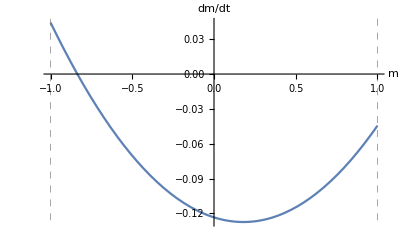

./Downloads/sol.pdf

```mathematica
(***** Edge Penalty *****)
μ=1./L;
ρ = 500;
ζ=ρ*μ;
(* Plots f(x) *)
f[x_]=-2*μ*x-ζ/(2*L)*(1-x^2)
p0=Plot[{f[x]},{x,-1,1},AxesLabel->{"m","dm/dt"},GridLines->{{-1,1}},GridLinesStyle->Directive[Gray, Dashed]]
Manipulate[Plot[{-2*μ*x-L/2*(1-x^2)},{x,-1,1},AxesLabel->{None,"dm/dt"},GridLines->{{-1,1}},GridLinesStyle->Directive[Gray, Dashed]],{μ,0.001,0.01,Appearance->"Labeled"},{ζ,0.001,0.01,Appearance->"Labeled"}];
Export["./Downloads/sol.pdf",p0]
```

```mathematica
(* Evaluate &
Plot analytical solution for Graph Density *)
d0=0.9;
sol=x[t]/.First@Chop[DSolve[{x'[t]==f[x[t]],x[0]==tospin[d0]},x,t]]
toedge[sol]//FullSimplify
lim = toedge[Limit[sol,t->Infinity]]
```

-(0.836071 (-5.9094+1. 2.71828^(0.250882 t)))/(4.13075+2.71828^(0.250882 t))

0.0819646+1/(0.984183+0.238258 ⅇ^(0.250882 t))

0.0819646

(4.94067-0.836071 ⅇ^(0.250882 t))/(4.13075+1. ⅇ^(0.250882 t))

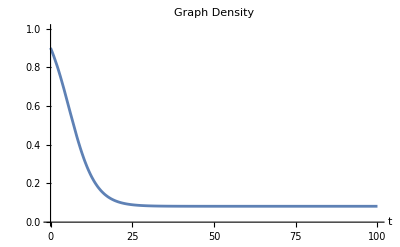

./Downloads/ms-1.pdf

```mathematica
m0 = tospin[d0];
m1 = 2*L/ρ +Sqrt[1+( 2*L/ρ)^(2)];
m2 = 2*L/ρ -Sqrt[1+( 2*L/ρ)^(2)];
g[t_]=m2(1+(m1/m2-1)/(1+(m1-m0)/(m0-m2)Exp[2*μ*t*Sqrt[1+( 2*L/ρ)^(-2)]]))//Simplify


p1 = Plot[{toedge[g[t]]},{t,0,100},PlotStyle->{Directive[AbsoluteThickness[2],Opacity[1],Violet]},PlotLabel->Style["Graph Density",12],PlotRange->{{0,100},{0,1}}, AxesLabel->{t,None}]
(*p1 = Plot[{toedge[sol], lim,toedge[0]},{t,0,250},PlotStyle->{Directive[AbsoluteThickness[2],Opacity[1],Violet],Directive[AbsoluteThickness[2],Dashing[{.02,.02,.002, .02}], Orange],Directive[AbsoluteThickness[1],Dashed, Darker@Green]},PlotLegends->{Exact Solution, Asymptote, Randomness},PlotLabel->Style["Graph Density",12],AxesLabel->{t,None}]*)
Export["./Downloads/ms-1.pdf",p1]
```

```mathematica
asymfromDE[μ0_,ζ0_]:=
Module[{a=μ0,b=ζ0},
f0[x_]=-2*a*x-b/2*(1-x^2);
sol0=x[t]/.First@Chop[DSolve[{x'[t]==f0[x[t]],x[0]==tospin[d0]},x,t]];
lim0 = Limit[sol0,t->Infinity];
lim0
]
asym[μ0_,ζ0_]:=
Module[{a=μ0,b=ζ0 },
f0[x_]=-2*a*x-b/2*(1-x^2);
asymvalue=x/.Solve[f0[x]==0,x][[1]];
asymvalue
]
asym[0.008,0.015]
μ0=Range[0.01,0.1,0.01]
ζ0=Range[0.1,0.8,0.05]
spindensity = Table[asym[μ0[[i]],ζ0[[j]]],{i,1,Length[μ0]},{j,1,Length[ζ0]}];
```

-0.395447

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8}

```mathematica
(* PLOT - Asymptotic Graph Density in the Parameter Space *)
{xticks,yticks}=MapIndexed[{#2[[1]],#}&,#]&/@{μ0,ζ0}
minmax = MinMax[toedge[spindensity]];

p2=MatrixPlot[toedge[spindensity],ColorFunction->ColorData[{"TemperatureMap",minmax}],ColorFunctionScaling->False,PlotLabel->Style["Asymptotic Graph Density, N=16",12] , PlotLegends->Automatic,FrameTicks->{MapAt[ScientificForm@#&,xticks,{All,2}],MapAt[Rotate[ScientificForm@#,45 Degree]&,yticks,{All,2}]},FrameLabel->{"μ","φ"}]
Export["./Downloads/ms-2.pdf",p2]
```

{{{1,0.01},{2,0.02},{3,0.03},{4,0.04},{5,0.05},{6,0.06},{7,0.07},{8,0.08},{9,0.09},{10,0.1}},{{1,0.1},{2,0.15},{3,0.2},{4,0.25},{5,0.3},{6,0.35},{7,0.4},{8,0.45},{9,0.5},{10,0.55},{11,0.6},{12,0.65},{13,0.7},{14,0.75},{15,0.8}}}

-Graphics-

./Downloads/ms-2.pdf